### DSC 101: Wed 18 Sep

#### Commands covered

Read the “Lesson” below. These are mathematical commands not explained in Wolfram, An Elementary Introduction to the Wolfram Language

##### Important:

```mathematica
/.,->(* -> is hyphen plus greater-than *)
Solve, NSolve
FindRoot
Plot,ContourPlot
ReplaceAll,Rule
```

##### Secondary:

```mathematica
Reals, Integers, Complexes (* domains; not commands *)
Root,N (* we have seen N in class; look it up *)
FullSimplify
```

##### Unimportant

```mathematica
MaxRoots, InfiniteLine
```

#### Lesson (to be done before class)

There will be a quiz on using the important commands at the beginning of class.

##### The documentation center

First take some time to familiarize yourself with the structure of the documentation pages of basic commands. For instance, for Solve[], a command we will be using (web link: ["http://reference.wolfram.com/language/ref/Solve.html"](http://reference.wolfram.com/language/ref/Solve.html)).

In the web version, the page for the command sits inside a couple of frames. At the very top, there is a header for the Wolfram company; below that, a Documentation Center header; finally, next is the documentation page for the command. If you have installed the documentation on your computer, the first two headers will be missing.

The documentation itself had a header with the kind of page indicated inside a blue rectangle on the left. It should read “BUILT-IN SYMBOL” for a command like Solve[]. Toward the right will be drop-down menus with links to related documentation pages. These vary from command to command.

The first important segment of the documentation is contained in a light blue rectangle. It contains “paradigms” of common uses of the command. They indicate the main things you can learn how to do on this page. Once you’re somewhat familiar with a command, they are a quick reminder of how to use, which argument comes first, which is second, and so forth.

The next section is called “Details and Options.” You need to click on it to see what it contains. It’s difficult to describe the importance of this section. Sometimes the details are arcane and hard to understand. Sometimes they’re crucial. For a beginner, I would say that if something is not working how you thought it would, you might skim through it to see if anything seems related. If so, read it and try to apply it to your problem. If you cannot figure it out, ask someone, like me.

The next section, “Examples,” comprises several subsections. The most important at this point will be “Basic Examples.” These examples show how the command works in basic applications. “Scope” shows the range of problems the command can address. “Generalizations & Extensions,” “Applications,” and “Properties & Relations” give more examples organized according to those titles. They tend to be overlapping categories, and it’s not worth worrying about what the exact differences are. The second “Options” describes the options for the command. For some commands, like Plot[], beginning users often need to use options to get the output they want. For others, like Solve[], they almost never use options. The plotting commands generally have too many options for a beginning to tackle. Sometimes typing = with a description leads you to the option you need to read about:

WolframAlphaQueryParseResults

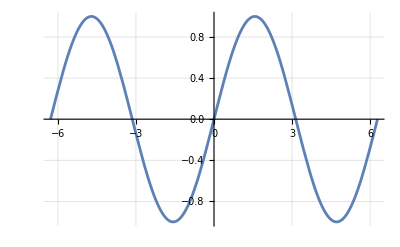

To learn Plot[], I often skimmed the example until I found something close to what I wanted. Then I tried to modify the example to do exactly what I wanted.

Below the “Examples” is the “See Also” section. Sometimes the first command you look up isn’t exactly the one you want. In this section are links to related commands, and you may find the one you’re looking for here.

Next are links to other related resources. “Tech Notes” are tutorials that go through a topic instead of focusing on a single command. “Guides” have links to commands and other resources related to the subjects in their titles.

##### The documentation search bar

There are two kinds of searches that it will perform: Search for a command page and search for pages related to the keyword(s) you type in. If you type in one word and it matches a command, you’ll get the page for that command. Otherwise, you will get a list of related documentation pages. It is case-sensitive! Searching for “Solve” gets you the page for Solve[]. Searching for “solve” gets you pages related to solving all sorts of things. You can also use a web search engine to find Wolfram documentation. Of course, if you search for “solve,” you probably will need to include other keywords like “Mathematica” or “Wolfram Language.”

##### Some basic “solvers”

Look up the documentation pages of these basic “solvers”:

```mathematica
Solve, NSolve,FindRoot
Plot,ContourPlot
```

Four of them, excluding Plot[], solve equations, with ContourPlot[] showing a graphical solution. Recall that equation use a double-equals: lhs==rhs. From the “Basic Examples,” you should be able to figure out how to write code to solve the exercises at the end. Some further notes on solutions returned by Solve[], NSolve[], and FindRoot[] are added below.

The first argument of a solver is a function, equation, or system of equations. The second argument specifies the variable of variables. If appropriate, the interval or starting value of the variable will need to be specified, too. In some cases, like ContourPlot[], you need two variable specifications (the second and third arguments).

For a system of equations, and list of equations and equations connected by And[] are considered equivalent, even though the code is not identical. Mathematica sometimes changes the code on you. Example of equivalent systems:

```mathematica
{x^2+y^2==5,y==x^2-3}
x^2+y^2==5&&y==x^2-3
```

##### Using solutions

To use a solution, you need to apply the solution with ReplaceAll[]. Look up the documentation page  for it. (Some of its basic examples touch on things we have not gotten to, so ignore the example that mentions “pattern.”)  A solution is constructed using Rule[], which is normally written variable -> value, where the arrow is typed by hyphen followed by a greater-than sign. It represents a substitution rule in which the variable is to be replaced by the value (in all occurrences of the variable).

Solve[] and NSolve[] return a solution set, represented by a List of solution. A solution has the form of a list of rules, one for each variable:

```mathematica
{v1->val1,v2->val2,...}
```

For instance:

```mathematica
sol=Solve[{x^2+y^2==5,y==x^2-3},{x,y}]
```

{{x→-2,y→1},{x→-1,y→-2},{x→1,y→-2},{x→2,y→1}}

Then First[sol] is the first solution,  Last[sol] is the last solution, and  sol[[3]] is the third solution. To plug in the last solution use ReplaceAll[], which is abbreviate “/.”:

```mathematica
{x^2+y^2==5,y==x^2-3}/.Last[sol]
```

{True,True}

We can plug it into any expression:

```mathematica
x^3+y^3/.Last[sol]
```

9

We can plug in all solutions at once, and we will obtain a list of values, one for each solution in order:

```mathematica
x^3+y^3/.sol
```

{-7,-9,-7,9}

Note that when we applied a single solution Last[sol], we got number, and when we applied the full solution set sol, we got a list. that is, a set of values.

##### Some notes on solvers

For Solve[] and NSolve[], the variable specification is just the variable or List of variables.

For FindRoot[], the variable specification is a list, {variable, start}, of the variable and the start value, or a List of such specifications:

```mathematica
FindRoot[t^2+t- Cos[t],{t,0.1}]
```

{t→0.550009}

```mathematica
FindRoot[{x^2+y^2==5,y==x^2-3},{{x,1.1},{y,1.2}}]
```

As mentioned earlier, ContourPlot[] needs to variable specification (each as separate arguments, not in a List):

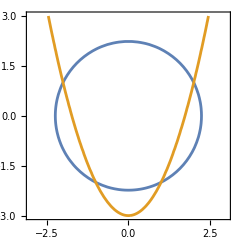

```mathematica
ContourPlot[{x^2+y^2==5,y==x^2-3},{x,-3,3},{y,-3,3}]
```

#### Exercises

Find all exact solutions to x^4-4x+3=0.

```mathematica
Solve[x^4-4x+3==0,x]
```

{{x→1},{x→1},{x→-1-ⅈ √2},{x→-1+ⅈ √2}}

Find the exact real solutions to x^4-4x+3=0.

```mathematica
Solve[x^4-4x+3==0,x,Reals]
```

{{x→1},{x→1}}

Find all approximate solutions to x^4-4x+3=0.

```mathematica
NSolve[x^4-4x+3==0,x]
```

{{x→-1.+1.41421 ⅈ},{x→-1.-1.41421 ⅈ},{x→1.},{x→1.}}

Find the approximate real solutions to x^4-4x+3=0.

```mathematica
NSolve[x^4-4x+3==0,x,Reals]
```

{{x→1.},{x→1.}}

Find an approximate solution to Tan[x]=x near x=7.5.

```mathematica
FindRoot[Tan@x==x,{x,7.5}]
```

{x→7.72525}

Solve a e^kx=p for real values of x.

```mathematica
Solve[a*Exp[k*x]==p,x,Reals]
```

{{x→ConditionalExpression[Log[p/a]/k, (a>0&&p>0)||(a<0&&p<0)]}}

Graphically show approximately the values of x where the graphs of 2 x^4+x^3+8x sin(2x) and x^4-x^2 intersect

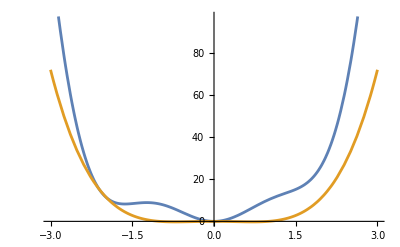

```mathematica
Plot[{(2x^4+x^3+8x*Sin@(2x)),(x^4-x^2)},{x,-3,3}]
```

Try to find the exact values of x where the graphs of 2 x^4+x^3+8x sin(2x) and x^4-x^2 intersect; comment on your success, given the result in exercise 7.

```mathematica
Solve[{2x^4+x^3+8x Sin[2x]==x^4-x^2},{x}]
```

It doesn’t work because it uses inverse functions to solve and can’t find all the solutions.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0}}

Use a simple NSolve[] command to try to find the approximate values of x where the graphs of 2 x^4+x^3+8x sin(2x) and x^4-x^2 intersect; comment on your success, given the result in exercise 7.

```mathematica
NSolve[{2x^4+x^3+8x Sin[2x]==x^4-x^2},{x}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.}}

Use FindRoot[] to find the approximate values of all x where the graphs of 2 x^4+x^3+8x sin(2x) and x^4-x^2 intersect; see exercise 7.

```mathematica
FindRoot[{2x^4+x^3+8x Sin[2x]==x^4-x^2},{x}]
```

FindRoot::srect: Value x in search specification {x} is not a number or array of numbers.

```mathematica
FindRoot[{2 x^4+x^3+8 x Sin[2 x]==x^4-x^2},{x,-1.9}]
FindRoot[{2 x^4+x^3+8 x Sin[2 x]==x^4-x^2},{x,0}]
```

{x→-1.97185}

{x→0.}

How can you be sure whether you found all the solutions in exercises 7–10?

I’m sure because I only saw two intercepts on the graph.

Graphically show the points of intersection of a circle of radius 1 centered at the origin and the graph of y=2Sin[4x].

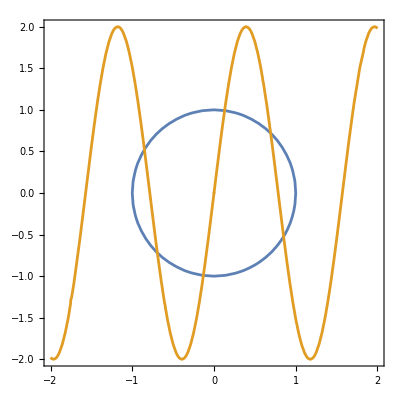

```mathematica
ContourPlot[{x^2+y^2==1,y==2Sin[4x]},{x,-2,2},{y,-2,2}]
```

Find the points of intersection of a circle of radius 1 centered at the origin and the graph of y=2Sin[4x]. Use N[] to convert the solutions to approximate numerical values. (Hint: Solve the system over the real numbers.)

```mathematica
N[Solve[{x^2+y^2==1,y==2Sin[4x]},{x,y},Reals]]
```

{{x→-0.85168,y→0.524063},{x→-0.693236,y→-0.720711},{x→-0.129683,y→-0.991556},{x→0.129683,y→0.991556},{x→0.693236,y→0.720711},{x→0.85168,y→-0.524063}}

Find the approximate coordinates of the points of intersection of a circle of radius 1 centered at the origin and the graph of y=2Sin[4x].

```mathematica
NSolve[{x^2+y^2==1,y==2Sin[4x]},{x,y},Reals]
```

{{x→-0.85168,y→0.524063},{x→-0.693236,y→-0.720711},{x→-0.129683,y→-0.991556},{x→0.129683,y→0.991556},{x→0.693236,y→0.720711},{x→0.85168,y→-0.524063}}

Consider the solutions found in exercise 12. Plug the last solution into the expression y^2/4+cos^2(4x) and use N[] to find its approximate numerical value.

```mathematica
sol=Solve[{x^2+y^2==1,y==2Sin[4x]},{x,y},Reals];
val=y^2/4+Cos[4x]^2/.Last@sol
N[val]
```

Cos[4 ]^2+Sin[4 ]^2

1.

Consider the solutions found in exercise 12. Plug all the solutions into the expression x^2+4-4cos^2(4x) and use FullSimplify[] on the list of values. Explain the simplicity of the result.

```mathematica
sol=Solve[{x^2+y^2==1,y==2Sin[4x]},{x,y},Reals];
x^2+4-4Cos[4x]^2/.sol;
FullSimplify[%]
```

{1,1,1,1,1,1}

##### Answers

Find all exact solutions to x^4-4x+3=0.

```mathematica
Solve[x^4-4x+3==0,x]
```

Find the exact real solutions to x^4-4x+3=0.

```mathematica
Solve[x^4-4x+3==0,x,Reals]
```

Find all approximate solutions to x^4-4x+3=0.

```mathematica
NSolve[x^4-4x+3==0,x]
```

Find the approximate real solutions to x^4-4x+3=0.

```mathematica
NSolve[x^4-4x+3==0,x,Reals]
```

Find an approximate solution to Tan[x]=x near x=7.5.

```mathematica
FindRoot[Tan[x]==x,{x,7.5}]
```

{x→7.72525}

Solve a e^kx=p for real values of x.

```mathematica
Solve[a Exp[k*x]==p,x,Reals]
```

Graphically show approximately the values of x where the graphs of 2 x^4+x^3+8x sin(2x) and x^4-x^2 intersect.

Most straightforward, but maybe not best:

```mathematica
Plot[{2x^4+x^3+8x Sin[2x],(x^4-x^2)},{x,-3,3}]
```

A little better:

```mathematica
Plot[(2x^4+x^3+8x Sin[2x])-(x^4-x^2),{x,-3,3}]
```

Shows the values of x best but does not show these are the only roots:

```mathematica
Plot[(2x^4+x^3+8x Sin[2x])-(x^4-x^2),{x,-2.3,0.5}]
```

Combining the last two makes for the best answer. You should keep in mind what is to be shown. If it takes two plots to show it all, use two plots.

Try to find the exact values of x where the graphs of 2 x^4+x^3+8x sin(2x) and x^4-x^2 intersect; comment on your success, given the result in exercise 7.

```mathematica
Solve[{2x^4+x^3+8x Sin[2x]==x^4-x^2},{x}]
```

Use a simple NSolve[] command to try to find the approximate values of x where the graphs of 2 x^4+x^3+8x sin(2x) and x^4-x^2 intersect; comment on your success, given the result in exercise 7.

```mathematica
NSolve[{2x^4+x^3+8x Sin[2x]==x^4-x^2},{x}]
```

Use FindRoot[] to find the approximate values of all x where the graphs of 2 x^4+x^3+8x sin(2x) and x^4-x^2 intersect; see exercise 7.

There are three solutions, so you need three commands:

```mathematica
FindRoot[2x^4+x^3+8x Sin[2x]==x^4-x^2,{x,0}]
```

```mathematica
FindRoot[2x^4+x^3+8x Sin[2x]==x^4-x^2,{x,-1.9}]
```

```mathematica
FindRoot[2x^4+x^3+8x Sin[2x]==x^4-x^2,{x,-2.2}]
```

How can you be sure whether you found all the solutions in exercises 7–10?

If we solve for the sine term we get
	8x sin(2x)=-x^4-x^3-x^2,
which implies
	8 sin(2x)=-x^3-x^2-x,
The left-hand side Abs[8sin(2 x)]<8 since sines and cosines stay between ±1. The right-hand side Abs[-x^3-x^2-x]=Abs[x](x^2+x+1), since x^2+x+1 has no roots and is positive. If x is less than -3 or greater than 2, then the right-hand side is greater than 21 or 14 respectively.

Graphically show the points of intersection of a circle of radius 1 centered at the origin and the graph of y=2Sin[4x].

```mathematica
ContourPlot[{x^2+y^2==1,y==2Sin[4x]},{x,-2,2},{y,-2,2}]
```

Find the points of intersection of a circle of radius 1 centered at the origin and the graph of y=2Sin[4x]. Use N[] to convert the solutions to approximate numerical values. (Hint: Solve the system over the real numbers.)

```mathematica
sol=Solve[{x^2+y^2==1,y==2Sin[4x]},{x,y},Reals]
N[sol]
```

Find the approximate coordinates of the points of intersection of a circle of radius 1 centered at the origin and the graph of y=2Sin[4x].

```mathematica
NSolve[{x^2+y^2==1,y==2Sin[4x]},{x,y},Reals]
```

Consider the solutions found in exercise 12. Plug the last solution into the expression y^2/4+cos^2(4x) and use N[] to find its approximate numerical value.

```mathematica
sol=Solve[{x^2+y^2==1,y==2Sin[4x]},{x,y},Reals];
val=y^2/4+Cos[4x]^2/.Last@sol
N[val]
```

Consider the solutions found in exercise 12. Plug all the solutions into the expression x^2+4-4cos^2(4x) and use FullSimplify[] on the list of values. Explain the simplicity of the result.

```mathematica
sol=Solve[{x^2+y^2==1,y==2Sin[4x]},{x,y},Reals];
x^2+4-4Cos[4x]^2/.sol;
FullSimplify[%]
```